# Numerical solution of the 2D Schrödinger equation

Bernd Thaller

```mathematica
$starttime=AbsoluteTime[];
{$Version,Date[]}
```

{11.3.0 for Microsoft Windows (64-bit) (March 7, 2018),{2018,4,25,15,4,24.2578023}}

## Preparations

For the numerical calculation we need the external application "QuantumKernel":

```mathematica
Needs["VQM`QuantumKernel`"]
```

For the graphical representation of the complex-valued wave function in two dimensions we use the package "ComplexPlot".

```mathematica
Needs["VQM`ComplexPlot`"]
```

The following command helps us get rid of unwanted error messages:

```mathematica
Off[Arg::indet];
```

## The initial function

### Definition of a Gaussian function

Our initial function will be a Gaussian wave packet. There are several parameters describing the physical properties of the initial state:

```mathematica
pos = {-3.,-3.};    (* average position at t=0 *)
mom = {4.,4.};      (* average momentum *)
a = 1.;             (* parameter for uncertainty in position space *)
```

We define the Gaussian function as

```mathematica
Gauss[x0_,y0_,kx_,ky_,a_] := Compile @@ 
   {{x,y}, Simplify[(a/Pi)^(1/2) Exp[I(kx x+ky y)]*
          Exp[-a ((x-x0)^2+(y-y0)^2)/2]]};
```

and obtain a compiled version just by calling

```mathematica
f=Gauss[pos[[1]], pos[[2]] ,mom[[1]], mom[[2]], 1];
```

Next, we produce a table of complex values, representing the initial function through the values at a grid of space points. The grid is a rectangular array of points defined by

```mathematica
numleft  = {-7.,-7.}; (* lower left corner *)
numright = {7.,7.};   (* upper right corner *)
dx = 0.14;            (* step size *)
```

The following command calculates the matrix of values. Note the order in which the x- and y-arguments are calculated:

```mathematica
psi0 = Table[f[x,y],
   {y,numleft[[2]]+dx/2,numright[[2]]-dx/2,dx},
   {x,numleft[[1]]+dx/2,numright[[1]]-dx/2,dx}];
```

### Plot of the initial function

We can make this array visible using the package ComplexPlot:

```mathematica
QListComplexDensityPlot[psi0,Mesh->False,DataRange->{{-7,7},{-7,7}},QSphereRadius->1/3.]
```

-Graphics-

### Passing values to QuantumKernel

The next step is the initialization: The package QuantumKernel provides the command QNewFunction for the purpose of passing values from Mathematica to the external routines.

```mathematica
psi = QNewFunction[Re[psi0], Im[psi0]]
```

QFunctionObject[3]

The array of values which represents the initial function is passed to the "QuantumKernel". The quantum kernel returns a "function object" which is referred to as psi.

Attention: Only numerical values can be sent to QuantumKernel. You have to be sure that psi0 contains only numerical values (no integers or symbolic expressions).

Note: The result of the numerical calculation will be stored in the same function object "psi". Whenever we want to repeat the calculation, we have to reissue the command above.

## QuantumKernel commands for function objects

### Some Mathematica commands provided by QuantumKernel

QNewFunction[arrays]

Generates a function object in QuantumKernel by passing the values from one or several arrays of real numbers.QuantumKernel returns a reference to the function object to Mathematica. Here every array is a one-, two-, or three-dimensional table of real numbers.

QDisposeFunction[ref_]

Disposes the numerical data contained in the function object which is referred to as 'ref'.

QGetFunctionInfo[ref_]

Get information about the function object with reference 'ref'.

QGetArray[ref_]

Transfers the numerical data contained in the function object 'ref' from QuantumKernel to Mathematica.

### Examples:

Above, we have defined the function object psi, using QNewFunction. This says that psi is a function object consisting of two arrays of 100x100  numerical data:

```mathematica
QGetFunctionInfo[psi]
```

{100,100,2}

This gives the numerical values stored in psi back to Mathematica.

```mathematica
psi1=QGetArray[psi];
```

psi1 is now a list of two arrays. We can make a single complex array out of these values:

```mathematica
psi2 = psi1[[1]] + I psi1[[2]];
```

Apart from numerical (finite precision) errors, psi2 is identical with psi0. Within QuantumKernel, the numerical values are stored with single precision. We can check this as follows.

```mathematica
Max[Abs[(psi2 - psi0)]]
```

2.70615×10^-8

## The potential

The potential, like the wave function, is passed to quantum kernel as a table of complex numerical values. For our example, we choose a smooth potential barrier along the main diagonal of the square region. The height of the barrier is determined from the kinetic energy of the wave packet.

```mathematica
Emean = mom.mom/2;
potfnc = Compile[{x, y}, Emean/Cosh[2(x+y)]];
```

The shape of the potential is best visualized with a contour plot:

```mathematica
ContourPlot[potfnc[x,y],{x,-7,7},{y,-7,7},PlotPoints→100,PlotRange→All, 
Contours→3]
```

-Graphics-

As before, we generate a table of numerical values by evaluating the potential at the grid points:

```mathematica
V0 = Table[potfnc[x,y],
      {y,numleft[[2]]+dx/2,numright[[2]]-dx/2,dx},
      {x,numleft[[1]]+dx/2,numright[[1]]-dx/2,dx}];
```

Finally, we send these values to QuantumKernel by generating a function object

```mathematica
V = QNewFunction[Re[V0],Im[V0]];
```

Attention: Since QuantumKernel accepts complex potentials, the values have to be passed as an array of complex numbers. In our case the imaginary part is equal to zero.

## The Schrödinger operator

Now we can define an operator object, which defines the generator of the time evolution. In QuantumKernel, we can generate several types of operator objects. Here we discuss the Schrödinger equation in two dimensions

ⅈ∂/(∂t)ψ(x,t) = -1/(2m)(∂^2/(∂x^2)+∂^2/(∂y^2))ψ(x,t) + e V(x,t)ψ(x,t)

where m is the mass and e is the charge of the particle. Here

H = -1/(2m)(∂^2/(∂x^2)+∂^2/(∂y^2)) + e V(x,t)

is the Schrödinger operator.

The QuantumKernel command for defining a two-dimensional Schrödinger operator is

QSchroedinger2D[scalar_potential, vector_potential, domain_mask, mass, charge, step_size]

Here the arguments mean the following: scalar_potential is a reference to a function object representing the scalar potential in the Schrödinger equation.
Similarly, vector_potential represents a magnetic vector potential which can be used to describe an additional magnetic field. Insert "None" if there is no vector potential. domain_mask is a function object describing a domain with Dirichlet boundary conditions. The domain mask is a function object defined by a single two-dimensional array of real numbers. In this array, positive values define the region of the numerical simulation, with a Dirichlet boundary condition at the border of that region. The solution is always set equal to zero in the region where the domain mask has, negative values. This can be used to describe particles in a region surrounded by infinitely high potential barriers. If there is no domain mask, insert "None". In this case, Dirichlet boundary conditions are assumed at the borders of the rectangular numerical domain. The parameters mass, charge and dx can be used for scaling purposes. Here we always assume that mass = 1., charge = 1., and for the step size we simply insert dx.

For our example, we define

```mathematica
H = QSchroedinger2D[V,None,None,1.,1.,dx]
```

QOperatorObject[2]

QuantumKernel returns an "operator object", which gets the name "H" in Mathematica. The data structure in QuantumKernel represents a space-discretization of the differential operator.

```mathematica
QGetOperatorInfo[H]
```

{Type→Schroedinger2D,ScalarPotential→QFunctionObject[4],VectorPotential→None,Domain→None,Mass→1.,Charge→1.,Units→0.14}

The above command provides some information about the just defined operator object. We can also obtain a summary about the state of QuantumKernel with all objects defined so far:

```mathematica
QInfo[]
```

{{{QFunctionObject[1],{2001,2}},{QFunctionObject[2],{2001,2}},{QFunctionObject[3],{100,100,2}},{QFunctionObject[4],{100,100,2}}},{{QOperatorObject[1],{Type→Schroedinger1D,ScalarPotential→QFunctionObject[2],Mass→1.,Units→0.02}},{QOperatorObject[2],{Type→Schroedinger2D,ScalarPotential→QFunctionObject[4],VectorPotential→None,Domain→None,Mass→1.,Charge→1.,Units→0.14}}},{}}

## The time evolution

Having defined the generator of the time evolution, we can now calculate a time-step. QuantumKernel provides the command QTimeEvolution, which needs several parameters.

QTimeEvolution[operator_object, function_object, time_step, order, repetitions]

This command performs the time evolution generated by the Hamiltonian operator "operator_object". It evolves the initial function "function_object" for the time repetitions*time_step. The parameter "order" is a positive integer describing the order of the method. The continuous time-evolution exp[i(dt)H] for a small time interval dt is approximated by discrete steps giving an approximation of order O((dt)^order) for the continuous time-evolution. Higher orders of course mean a better approximation, but also take a longer time to execute (because the time step dt is subdivided into smaller units). Note also that the accuracy is likewise limited by the spacial step size dx.

For our example, we define

```mathematica
dt = 0.01; ordr = 4; reps = 20;
```

Now we perform the time evolution of the initial wave function (=function object, referred to as "psi") for the time t=reps*dt:

```mathematica
QTimeEvolution[H, psi, dt, ordr, reps]
```

After performing this command, the function object "psi" contains the numerical data of the wave function at the time t=reps*dt = 0.2

```mathematica
psi1 = QGetArray[psi];
```

```mathematica
psi2 = psi1[[1]] + I psi1[[2]];
```

```mathematica
QListComplexDensityPlot[psi2,Mesh->False,DataRange->{{-7,7},{-7,7}},QSphereRadius->1/3.]
```

-Graphics-

Let us perform another series of time steps. Now the intial function "psi" is the wave function at time t=0.2

```mathematica
QTimeEvolution[H, psi, dt, ordr, 80]
```

```mathematica
psi1 = QGetArray[psi];
```

```mathematica
psi2 = psi1[[1]] + I psi1[[2]];
```

```mathematica
QListComplexDensityPlot[psi2,Mesh->False,DataRange->{{-7,7},{-7,7}},QSphereRadius->1/3.]
```

-Graphics-

This image shows the wave function at time t=1. It has already hit the potential barrier. The transmitted part starts to emerge behind the barrier.

## Getting the solution from QuantumKernel

If you don't want to use the nonstandard package ComplexPlot, you can plot just the absolute values of the wave function using a DensityPlot command. Here it is the fastest way to get just the absolute values of the wave function

```mathematica
abspsi=QGetAbsArray[psi];
```

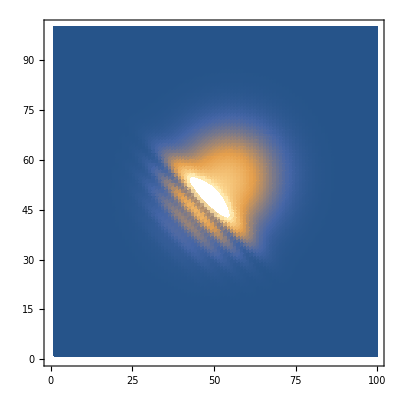

```mathematica
ListDensityPlot[abspsi,Mesh→False,PlotRange→{0,.4}]
```

With the following command you can obtain a density plot of the position probability density, i.e., of the absolute square of the wave function:

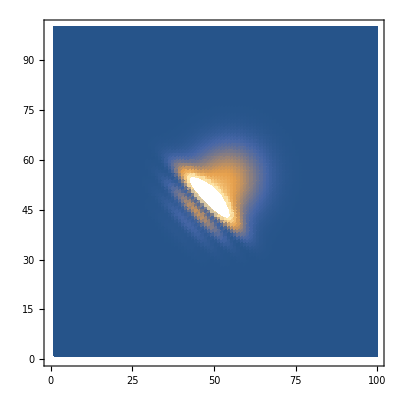

```mathematica
ListDensityPlot[abspsi^2,Mesh→False,PlotRange→{0,(.4)^2}]
```

For the next examples, we restore the initial function. We multiply the initial function by 3. This makes the wave function appear brighter in the following images.

```mathematica
psi = QNewFunction[3. Re[psi0], 3. Im[psi0]]
```

QFunctionObject[5]

A fast method of obtaining a color picture in Mathematica is to import the color information directly and generate a Graphics element using Raster:

RM: 25.6.2007:  Vielleicht sollte QGetColorArray direkt RGBColor->List beinhalten.

```mathematica
colors = QGetColorArray[psi];
```

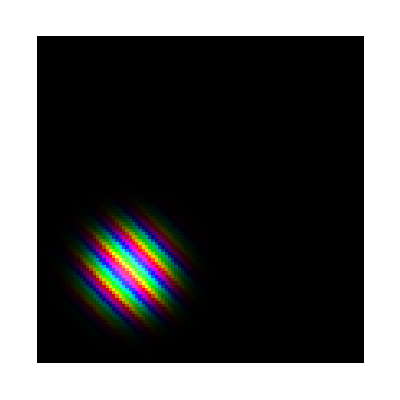

```mathematica
Graphics[Raster[colors/.RGBColor->List(*,ColorFunction->RGBColor*)]]
```

If you need proper tickmarks, you can use the command QColorArrayPlot provided by the package ComplexPlot

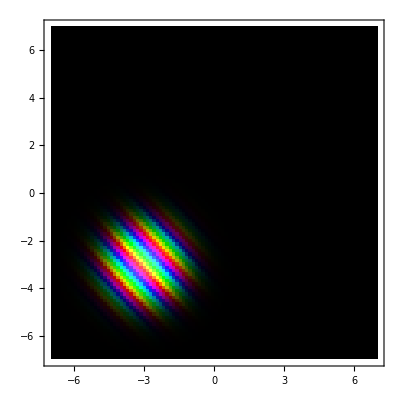

```mathematica
QColorArrayPlot[colors,DataRange->{{-7,7},{-7,7}},Mesh->False]
```

We can also obtain an array of gray values representing the probability density using the command

```mathematica
grays = QGetGrayArray[psi]/.GrayLevel->List;
```

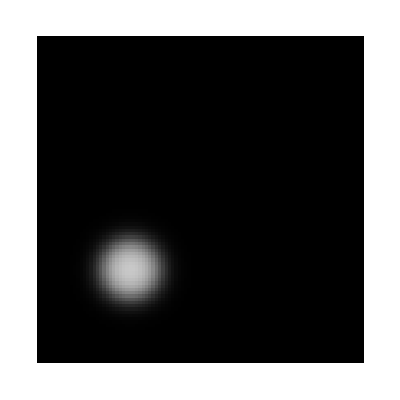

```mathematica
Graphics[Raster[grays]]
```

```mathematica
AbsoluteTime[]-$starttime
```

3.9557347